## Visualization

```mathematica
theEdgeInCoords = Table[{Green,Thickness[0.003],Line[{thepoints⟦skelLine⟦1⟧⟧,thepoints⟦skelLine⟦2⟧⟧}]},{skelLine,thelines}];
```

```mathematica
theBasicBalls=Table[{Opacity[0.5], degreeColor[theJ⟦i, 2⟧], Ball[theJ⟦i,4⟧,theJ⟦i,5⟧]},{i,Dimensions[theJ]⟦1⟧}];
```

```mathematica
theMergedBalls=Table[{Opacity[0.5], degreeColor[theJres⟦i, 2⟧], Ball[theJres⟦i,4⟧,theJres⟦i,5⟧]},{i,Dimensions[theJres]⟦1⟧}];
```

```mathematica
theMergedBalls2=Table[{Opacity[0.5], degreeColor[Length[theJres⟦i, 7⟧]], Ball[theJres⟦i,4⟧,theJres⟦i,5⟧]},{i,Dimensions[theJres]⟦1⟧}];
```

```mathematica
Manipulate[
	Show[Graphics3D[{
			If[showEdges,theEdgeInCoords],
			If[showBasicBalls,theBasicBalls],
			If[showMergedBalls,theMergedBalls]
			(*If[showMergedBalls2,theMergedBalls2]*)
		}]
	],
	{showEdges, {True, False}},
	{showBasicBalls, {True, False}},
	{showMergedBalls, {True, False}}
(*	{showMergedBalls2, {True, False}}*)
]
```

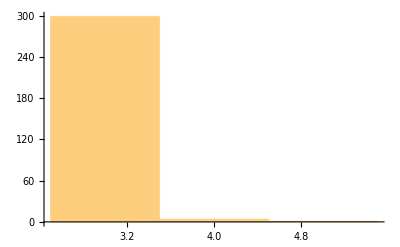

```mathematica
Histogram[theJ⟦;;,2⟧]
```

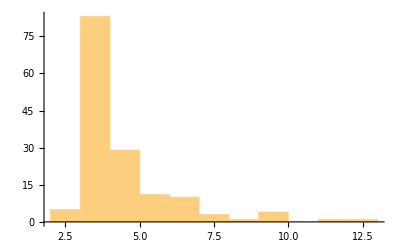

```mathematica
Histogram[theJres⟦;;,2⟧]
```

```mathematica
ps=SpherePoints[8];
o={0,0,0};
struct=Table[Line[{o,ps⟦i⟧}],{i,1,Length[ps]}];
Graphics3D[struct]
```

-Graphics3D-

```mathematica
points = SpherePoints[5];
i=5;
For[j =1, j≤ Length[points], j++,
	If[j≠ i,
		theAngle = computeAngle[{0,0,0},points⟦i⟧,points⟦j⟧];
		Print[theAngle];
	]
]
```

90.

90.

120.

120.